```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY201/sec_int_data/862nm.dat"]
```

{{1.59376,-0.182446},{1.5163,-0.182518},{1.45822,-0.175211},{1.41492,-0.180407},{1.36475,-0.171607},{1.33366,-0.158187},{1.2821,-0.160838},{1.25075,-0.160556},{1.2275,-0.177107},{1.20277,-0.177537},{1.18632,-0.171655},{1.16701,-0.197561},{1.14926,-0.298945},{1.12973,-0.5775},{1.10588,-inf},{1.11907,-0.615501},{1.13878,-0.388534},{1.30525,-0.199647},{1.35407,-0.239743}}

0.229416 (-3.12476+2.85578 -inf)+0.178327 (2.12422-2.64184 -inf) x

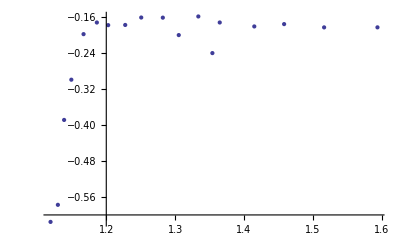

-Graphics-

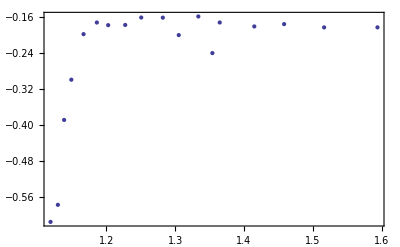

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```